## 2.1 Appetizer: Wigner’s Surmise

```mathematica
Clear[Hs,x1,x2,x3,λ,s,λs]
Hs={{x1,x3},{x3,x2}};
λs=Solve[λ^2-Tr[Hs]λ+Det[Hs]==0,λ]
s=λs[[2,1,2]]-λs[[1,1,2]]//FullSimplify
```

{{λ→1/2 (x1+x2-√(x1^2-2 x1 x2+x2^2+4 x3^2))},{λ→1/2 (x1+x2+√(x1^2-2 x1 x2+x2^2+4 x3^2))}}

√((x1-x2)^2+4 x3^2)

```mathematica
(* eq 2.3 *)
Clear[x1,x2,x3,r,θ,ψ]
Solve[{x1-x2==r Cos[θ],2x3==r Sin[θ],x1+x2==ψ},{x1,x2,x3}]
```

{{x1→1/2 (ψ+r Cos[θ]),x2→1/2 (ψ-r Cos[θ]),x3→1/2 r Sin[θ]}}

## Figure 2.1 Wigner’s surmise

1/2 ⅇ^(-(π s^2)/4) π s

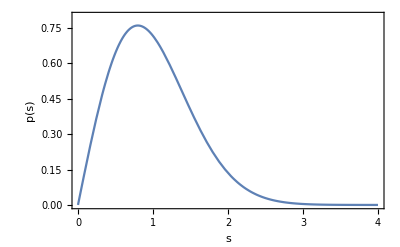

```mathematica
(*Integrate[s/2 Exp[-s^2/4],{s,0,∞}]*)
pbar=π s/2 Exp[-π s^2/4]
Plot[pbar,{s,0,4},PlotRange->{0,0.8},Frame->True,FrameLabel->{"s","p(s)"}]
```